# Rapport projekt inlämning 1

Oliver Rosvall, IX1307, orosvall@kth.se
David Berg Överby, IX1307, davbo@kth.se

Uppgift 1: Polynomekvation

## Sammanfattning

### Uppgift

Hitta lösningarna till polynomekvationen: x^5-2 x^4-19/4 x^3+31/4 x^2+11/2 x-15/2=0. 
Rita också grafen för polynomet och markera nollställen med en röd punkt.

### Resultat

För att lösa ekvationen x^5-2 x^4-19/4 x^3+31/4 x^2+11/2 x-15/2=0 måste vi räkna ut x värderna i ekvationen. Genom att anända vanlig alegrab får man lösningen på x-värderna x_1,x_2,x_3, x_4, x_5:

{-3/2,1,5/2,-√2,√2}

## Visualisering

### Graf över lösning

Nedan följer en graf på ekvationen och dess lösningar markerat i rött.

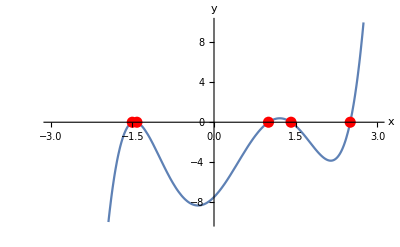

## Kod

Vi berättar för programet att F[x_] är polynomekvationen:

```mathematica
f[x_] =x^5 - 2*x^4 - (19/4)*x^3 + (31/4)*x^2 + (11/2)*x - 15/2
```

Sedan måste vi lösa ekvationen och samtidigt namnger vi lösningarna.

```mathematica
{x1, x2, x3, x4, x5} = x/.Solve [f[x] ==0, x]
```

Därefter användes följande kod för att rita grafen och dess lösningar.

```mathematica
p1 = Plot [f[x],{x,-10, 10},
PlotRange -> {{-3,3}, {-10,10}},
AxesLabel-> {"x", "y"},
Epilog->{PointSize[0.02],Red, Point[{{x1, f[x1]},{x2, f[x2]}, {x3, f[x3]}, {x4, f[x4]}, {x5, f[x5]}}]}]
```

Uppgift 2: Ekvation med absolutbelopp

## Sammanfattning

### Uppgift

Lös ekvationen |x-1|+|x+2|=3 och illustrera lösningsområdet grafiskt.

### Resultat

Med hjälp av Mathematica får vi följande lösning till absolutbeloppet. Det visar sig vara ett intervall mellan -2 till 1 för x-värdet.

-2≤x≤1

## Visualisering

### Lösning av ekvationen

Lösningen på ekvationen kan visualiseras på följande.

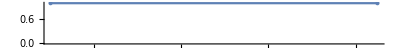

## Kod

```mathematica
ClearAll["`*"]
```

Inför givna data

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Definiera diff.ekvationer och begynnelsevillkor.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Lös diff.ekv.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Exempel för θ=45°

```mathematica
sol[45°]
```

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

Kurva för variabel vinkel

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

Funktion för sparklängd

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Exempel

```mathematica
len[45°]
```

Tabell för olik vinklar

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Noggrannare data kring maxvärdet.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

Sök maxvärde

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```

Uppgift 3: Bionomisk ekvation

## Sammanfattning

### Uppgift

Finn lösningen till ekvationen z^7=1-i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

### Resultat

Med hjälp av Mathematica får vi sju stycken lösningar. Samtliga lösninga visas nedan:

```mathematica
(1-ⅈ)^(1/7),-(-1)^(1/7)(1-ⅈ)^(1/7),(-1)^(2/7)(1-ⅈ)^(1/7),-(-1)^(3/7)(1-ⅈ)^(1/7),(-1)^(4/7)(1-ⅈ)^(1/7),-(-1)^(5/7)(1-ⅈ)^(1/7),(-1)^(6/7)(1-ⅈ)^(1/7)
```

## Visualisering

### Lösning av ekvationen

Nedan visas lösningarna i ett talplan.

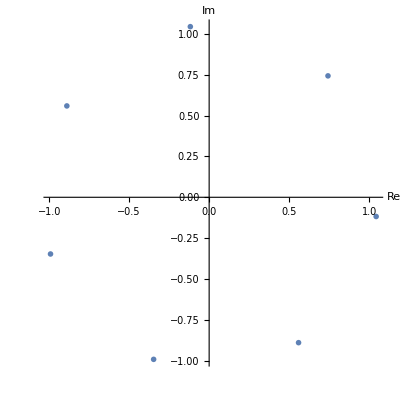

Det visar sig att punkterna är placerade i ett cirkulärt mönster i talplanet.

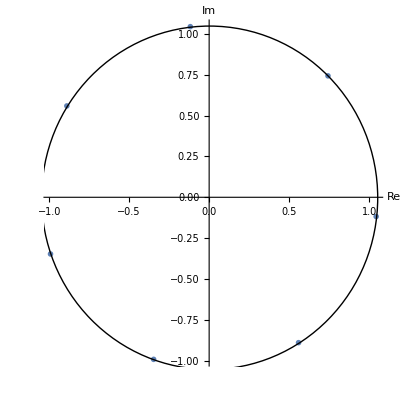

## Kod

För att lösa ekvationen använder vi oss av en solv funktion av ekvationen.

```mathematica
{z1,z2, z3, z4,z5, z6, z7}= z /. Solve [z^7 == 1 - I, z]
```

Därefter skapas en lista över lösningarna denna betecknas cn.

```mathematica
cn={z1,z2, z3, z4,z5, z6, z7}
```

Efter detta skapas en lista av olika talpar (Reella och imaginära), listan betäckans pp.

```mathematica
pp=Table[{Re[cn[[i]]], Im[cn[[i]]]}, {i,1,7}]
```

Slutligen används följande kod för att visualisera lösningspunkterna.

```mathematica
ListPlot[pp, AxesLabel->{"Re", "Im"}, AspectRatio->Automatic,PlotMarkers->{Automatic, Medium},Epilog->{ Circle[{0,0},  Abs[cn[[1]]]]}]
```

Uppgift 4 Akilles och sköldpaddan

## Sammanfattning

### Uppgift

Uppgift 4: Akilles och sköldpaddan är en av Zenons paradoxer. Antag att Akilles springer 10 gånger så fort som sköldpaddan. De båda skall tävla vem som först kommer i mål på 100 meter. Då sköldpaddan är långsammare än Akilles så får den ett försprång på 80 meter. Paradoxen är att när Akilles har sprungit dessa 80 meter, så har sköldpaddan kommit 8 meter, när Akilles har sprungit dessa 8 meter har sköldpaddan kommit 8 dm. Det resonemanget skulle leda till att Akilles aldrig kommer i kapp sköldpaddan. Undersök och förklara paradoxen, samt ta fram en lösning när Akilles faktiskt kommer i kapp sköldpaddan. Visa paradoxen både numeriskt och grafiskt.

Enhet för 1 meter = d
Slutmål distans uttryckt i meter d_end = 100
Tidsenhet per rörelse för Akilles och sköldpaddan = 10^(1-n)
Sköldpaddans hastighet  s_v = 8 10^(1 - n)
Akilles hastighet  a_v= 10 s_v*10^(1 - n)

Akilles startdistans a_d0 = 0
Skoldpaddans distans vid n_1= 88
Akilles Distans vid n_1 = 80
Avstånd mellan Akilles och sköldpaddan = d_Δ

### Resultat

I systemet som paradoxen målar upp finns ingen konstant enhet för tid.Det är istället det antal rörelser som Akilles och sköldpaddan har rört sig sedan början då distansenminskar logaritmiskt med antalet rörelser. Om man ska skriva ekvationen i författarens anda antar man att distansen mellan dem går mot 0.

8*10^(1-n)= d_Δ 
Där n är antalet rörelser  och d_Δ   är distansen mellan dem.

För en verklighet där tiden  är ett konstant värde blir resultatet annorlunda.
80n=8 n+80
            n=10/9
Där n är en konstant  tidsenhet som ökar med 1 för första rörelsen.

## Visualisering

### Paradoxens graf Y axeln är avståndet mellan dem, x axeln är antal rörelser

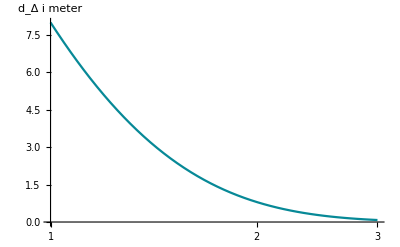

### Ekvationens graf Distans och tid för Akilles och sköldpaddan. -Graphics-

## Kod

```mathematica
Enhet för 1 meter = d
Slutmål distans uttryckt i meter Subscript[d, end] = 100
Tidsenhet per rörelse för Akilles och sköldpaddan = 10^(1-n)
Sköldpaddans hastighet  Subscript[s, v] = 8 10^(1 - n)
Akilles hastighet  Subscript[a, v]= 10 Subscript[s, v]*10^(1 - n)
Sköldpaddans startdistans Subscript[s, d0]= 80 
Akilles startdistans Subscript[a, d0] = 0
Skoldpaddans distans vid Subscript[n, 1]= 88
Akilles Distans vid Subscript[n, 1] = 80
Avstånd mellan Akilles och sköldpaddan = Subscript[d, Δ]
```

I systemet som paradoxen målar upp finns ingen konstant enhet för tid. Det är istället det antal rörelser som Akilles och sköldpaddan har rört sig sedan början n_0. 
då distansen  d_Δ minskar logaritmiskt med antalet rörelser n. 

Man kan endast måla upp paradoxen så som den är exakt skriven genom att visa d_Δ .

för 0 <= n
8*10^(1-n)== d_Δ

Ett godtyckliga världen för n illustrerar det minskande avståndet

```mathematica
n = 4
```

```mathematica
8*10^(1-n) ==d
```

```mathematica
Clear[n]
```

Och en grafisk lösning

```mathematica
8* 10^(1 - n) == d
```

```mathematica
LogLinearPlot[8*10^(1-n),{n, 1, 3}, AxesLabel-> HoldForm[Subscript[d, Δ] i meter]]
```

Då distansen går mot 0 d_Δ != 0 kommer Akilles aldrig komma ikapp sköldpaddan.

### Att lösa den här ekvationen i verkligheten

I verkligheten så finns det en variabel som ersätter paradoxens egna.

```mathematica
En konstant tidsenhet  = n
```

Då blir det enkelt att lösa.

a_d för n_0 = 0
s_d för n_0 = 80

då a_d för n_1 = 80
s_d för n_1 = 88

och a_v= 10 s_v

kan man skriva ekvationen

```mathematica
80n=8 n+80
```

```mathematica
Reduce[80n == 8n + 80,n]
```

och svaret är  n==10/9 eller 1,1

```mathematica
f[x_] = 80n
g[x_] = 8n + 80
```

```mathematica
Plot[{f[x], g[x]}, {n, 0, 2}, AxesLabel-> {"tid", "Distans"}, PlotLabels->{"Akilles", "Sköldpaddan"} ]
```

Hjälpmedel

## Hjälpmedel som vi tagit hjälp av

För att lösa dessa uppgifter har vi använt oss av webbsidan Wolframalpha, Wolfram Documentation och även kursmaterial från kursen IX1300.